```mathematica
(*run with CVnoisyStorageRates !! *)
```

```mathematica
(*Experimental Parameter *) 
CMloss[Γ_,μB_] := DiagonalMatrix[{1,1,Sqrt[1-μB],Sqrt[1-μB]}].Γ.DiagonalMatrix[{1,1,Sqrt[1-μB],Sqrt[1-μB]}] + DiagonalMatrix[{0,0,μB,μB}];
alphabet0=α0/0.1//N;
n = 2*10^5;  (* number of signals*) 
ϵA0=10^-7;   (* security epsilon *) 
δ = 0.1; (*the bin size in the discretization of the data*)
alphabet=2^10; (* the size of the alphabet for discretization *)
α=δ * alphabet/2;(*the cut-off parameter *)

CMexp1 = {{21.930581, 0.000000,-21.841251,0.000000},{0.000000,24.890632,0.000000,24.795180},{-21.841251,0.000000,21.930580,0.000000},{0.000000,24.795180,0.000000,24.890631}};
rEC= N[({436000,448000,460000,472000,478000,490000}*2)/(2*10^5)]
(* Parameter for the attackers memory *)
Nmax0=100; (*number of maximal photon numbers *)
eta0=0.75; (* transmission of QM *) 
betasimulation = 0.925;
Print["error correction: ", EC[δ,CMexp1,betasimulation]]

(* two graphs for different number of QM fractions *) 
ν0=0.001;
ν1=0.01;

rOTexp0={{0,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[1]],ν0,Nmax0,eta0]},{0.03,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[2]],ν0,Nmax0,eta0]},{0.06,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[3]],ν0,Nmax0,eta0]},{0.09,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[4]],ν0,Nmax0,eta0]},{0.12,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[5]],ν0,Nmax0,eta0]},{0.15,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[6]],ν0,Nmax0,eta0]}}
rOTexp1={{0,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[1]],ν1,Nmax0,eta0]},{0.03,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[2]],ν1,Nmax0,eta0]},{0.06,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[3]],ν1,Nmax0,eta0]},{0.09,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[4]],ν1,Nmax0,eta0]},{0.12,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[5]],ν1,Nmax0,eta0]},{0.15,rateOTgaussExp[δ,CMexp1,n,ϵA0,α,rEC[[6]],ν1,Nmax0,eta0]}}
```

{4.36,4.48,4.6,4.72,4.78,4.9}

error correction: 4.41112

{{0,0.222151},{0.03,0.192151},{0.06,0.162151},{0.09,0.132151},{0.12,0.117151},{0.15,0.0871509}}

{{0,0.187586},{0.03,0.157586},{0.06,0.127586},{0.09,0.097586},{0.12,0.082586},{0.15,0.052586}}

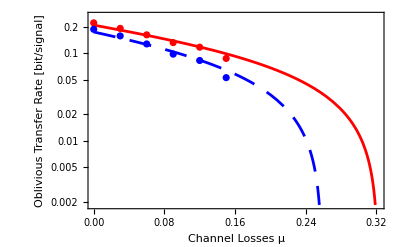

```mathematica
PlotExp=Show[LogPlot[{rateOTgauss[δ,CMloss[CMexp1,loss],betasimulation,2*10^5,ϵA0,α0,ν0,100,0.75],rateOTgauss[δ,CMloss[CMexp1,loss],betasimulation,2*10^5,ϵA0,α0,ν1,100,0.75]},{loss,0,0.35},PlotRange->{0,Automatic},PlotStyle-> {{Thickness[0.005],Red},{Thickness[0.005],Blue,Dashing[{0.04,0.0263}]}},LabelStyle->Directive[Black,FontSize->12],FrameStyle->Thickness[0.0035],Frame->{{True,True},{True,True}},FrameLabel->{"Channel Losses μ","Oblivious Transfer Rate [bit/signal]"},
BaseStyle->{FontFamily->"Times New Roman",FontSize->16}],
ListLogPlot[{rOTexp0,rOTexp1},PlotStyle->{Red,Blue, PointSize[Large]},BaseStyle->{FontFamily->"Times New Roman",FontSize->16}]]
```

```mathematica
Export["ExpPlot.pdf",PlotExp]
```

ExpPlot.pdf

```mathematica
(*Show[Plot[{rateOTgauss[0.2,CM[loss],0.93,2*10^5,ϵA0,α0,ν0,100,0.75],rateOTgauss[0.2,CM[loss],0.93,2*10^5,ϵA0,α0,ν1,100,0.75]},{loss,0,0.5},PlotRange->{0,Automatic},PlotStyle-> {{Thickness[0.005],Red},{Thickness[0.005],Blue,Dashing[{0.04,0.0263}]}},LabelStyle->Directive[Black,FontSize->12],FrameStyle->Thickness[0.0035],Frame->{{True,True},{True,True}},FrameLabel->{"Channel Losses μ","OT Rate"}], 
ListPlot[{rOTexp0,rOTexp1},PlotStyle->{Red,Blue, PointSize[Large]}]]*)
```